```mathematica
Clear["Global`*"];
startTime=SessionTime[];

TOL = 10^-8;
plutoRadius = 1195000`64; (* radius in meters *)

(* physical constants with increased arbitrary precision in mks units*)

NAvagadro = 6.02214129`64*10^23;  (* Avagadro's number *)
R = 8.3144621`64; (*J/mol K; universal gas constant*)
k = 1.3806488`64*10^-23; (* m^2kgs^-2K^-1; Boltzmann constant *)
G = 6.67384`64*10^-11; (* universal gravitational constant *)

αN2 =  1.71`64*10^-30;  (* m^3, mean polarizability of Subscript[N, 2] gas http://cccbdb.nist.gov/exp2.asp?casno=7727379 *)
μN2 = 0.0280134`64; (* kg; molar mass of Subscript[N, 2] *)

(* assumed properties of Pluto *)
p0 = 0.3`64; (* N/m^2; assumed surface pressure of Pluto == 3 microbars *)
T = 50.`64; (* K; assumed atmospheric temperature for isothermal model *)
MPluto = 1.29`64*10^22; (* kg; mass of Pluto *)

distToObserver = 
  5`64*10^12;(* TODO - average Pluto distance from Earth in m = 5*10^12 *)

(* make the atmosphere *)
layers = 100;
atmMin = plutoRadius;
atmMax = 1500000`64;
atmStep = (atmMax - atmMin)/layers;


(*local gravity as a function of r*)
Gravity[r_,M_]:=G*M/r^2;

(*barometric formula-pressure as a function of height*)
Barometric[p0_,M_,h_,T_,r0_,Mplanet_]:=p0 E^((-M Gravity[h+r0,Mplanet] h)/(R T));

SetAtmProperty[startValue_,stopValue_,numShells_]:=Module[{},
If[
startValue==stopValue, (* no variation *)
ConstantArray[startValue,numShells],

(* linear variation *)
Range[startValue,stopValue,(stopValue-startValue)/(numShells-1)]
]
];

SlopeInterceptFrom2Pts[x1_,y1_,x2_,y2_]:=Module[{m,b},
m = (y1-y2)/(x1-x2);
b=y1-m x1;
Return[{m,b}];
];
```

```mathematica
MakeAtmosphereSection2[r0_,r1_,MPlanet_,sectionShells_,T0_,T1_,μ0_,μ1_,P0_]:=Module[{radii,temps,mmw,pressures,nDens,dP,mμ,bμ,mT,bT,P,r,i},
(* set initial (or complete) values *)
{mμ,bμ}=SlopeInterceptFrom2Pts[r0,μ0,r1,μ1];
{mT,bT}=SlopeInterceptFrom2Pts[r0,T0,r1,T1];
radii = SetAtmProperty[r0,r1,sectionShells];
mmw = SetAtmProperty[μ0,μ1,sectionShells];
temps = SetAtmProperty[T0,T1,sectionShells];
pressures = {P0}; (* calculate initial pressures *)
nDens = {P0/(k temps[[1]])}; (* calculate initial number density *)
dP = {nDens[[1]] mmw[[1]]}; (* calculate initial dP/dr *)

Do[
AppendTo[pressures,Re[DSolveValue[{P'[r]== -((mμ r +bμ)/(mT r +bT)) (P[r]/R) ((G MPlanet)/r^2),P[r0]==P0},P[radii[[i]]],r]]];
AppendTo[nDens,pressures[[i]]/(k temps[[i]])];
AppendTo[dP,nDens[[i]] mmw[[i]]];,
{i,2,Length[radii]}
];
Return[{radii,temps,mmw,pressures,nDens}];
];

(* joins several atmosphere sections consecutively (no additional ordering or continuity assumptions *)
(* takes a list of atmosphere sections (list of lists) as an argument *)
JoinAtmosphereSections[sections_]:=Module[{radii,temps,mmw,pressures,nDens},
radii = {};
temps = {};
mmw = {};
pressures = {};
nDens = {};
Do[
radii= Join[radii,sections[[i,1]]];
temps=Join[temps,sections[[i,2]]];
mmw=Join[mmw,sections[[i,3]]];
pressures=Join[pressures,sections[[i,4]]];
nDens=Join[nDens,sections[[i,5]]];,
{i,1,Length[sections]}
];
Return[{radii,temps,mmw,pressures,nDens}];
];

r0=plutoRadius;
r1=1.25`64*plutoRadius;
r2 = 1.5`64*plutoRadius;
MPlanet=MPluto;
sectionShells=100;
T0=50;
T1=100;
T2 = 100;
M0=μN2;
M1=μN2;
M2=μN2;
nDens0=10^21;
μ0=μN2;
μ1=μN2;
```

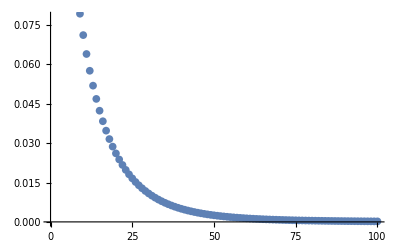

```mathematica
P0=0.2;
{mμ,bμ}=SlopeInterceptFrom2Pts[r0,μ0,r1,μ1];
{mT,bT}=SlopeInterceptFrom2Pts[r0,T0,r1,T1];
radii = SetAtmProperty[r0,r1,sectionShells];
mmw = SetAtmProperty[μ0,μ1,sectionShells];
temps = SetAtmProperty[T0,T1,sectionShells];
pressures = {P0}; (* calculate initial pressures *)
nDens = {P0/(k temps[[1]])}; (* calculate initial number density *)
dP = {nDens[[1]] mmw[[1]]}; (* calculate initial dP/dr *)

ListPlot[MakeAtmosphereSection2[r0,r1,MPluto,sectionShells,T0,T1,μN2,μN2,0.2][[4]]]
```